```mathematica
data={{0,11.26},{100,11.26},{200,11.26},{300,11.25},{400,11.24},{500,11.22},{600,11.21},{700,11.19},{800,11.16},{900,11.14},{1000,11.11},{1100,11.07},{1200,11.04},{1221.5,11.03}};
```

```mathematica
nlm=NonlinearModelFit[data, a -b x^2,{a,b},x]
```

FittedModel[11.2633-1.55946×10^-7 x^2]

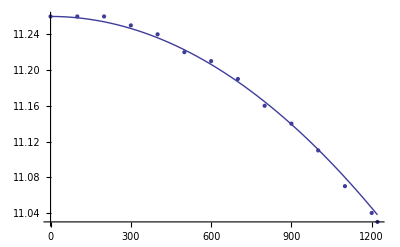

```mathematica
Show[ListPlot[data],Plot[11.26 Cos[x/(1.6π 1221.5)],{x,0,1221.5}]]
```

```mathematica
a=E;
b=π;
p=3^π;
```

```mathematica
v[r]:=a-b r^2
Integrate[r/Sqrt[v[r]^2 r^2-p^2 v[r]^4],r]
```

((ⅇ-π r^2) √(9^π ⅇ^2-r^2-2 9^π ⅇ π r^2+9^π π^2 r^4) ArcTan[(ⅇ+π r^2)/(2 √(ⅇ π) √(9^π ⅇ^2-r^2-2 9^π ⅇ π r^2+9^π π^2 r^4))])/(2 √(ⅇ π) √(r^2 (ⅇ-π r^2)^2-9^π (ⅇ-π r^2)^4))

```mathematica
((ⅇ-π r^2) √(-ⅇ^2+ⅇ^(2 π) r^2+2 ⅇ π r^2-π^2 r^4) (2 π+Log[π]-2 Log[ⅇ-π r^2]+2 Log[ⅇ^(1+π)+ⅇ^π π r^2+2 √(ⅇ π) √(-ⅇ^2+ⅇ^(2 π) r^2+2 ⅇ π r^2-π^2 r^4)]))/(4 √(ⅇ π) √(-(ⅇ-π r^2)^2 (ⅇ^2-ⅇ^(2 π) r^2-2 ⅇ π r^2+π^2 r^4)))
```

((ⅇ-π r^2) √(-ⅇ^2+ⅇ^(2 π) r^2+2 ⅇ π r^2-π^2 r^4) (2 π+Log[π]-2 Log[ⅇ-π r^2]+2 Log[ⅇ^(1+π)+ⅇ^π π r^2+2 √(ⅇ π) √(-ⅇ^2+ⅇ^(2 π) r^2+2 ⅇ π r^2-π^2 r^4)]))/(4 √(ⅇ π) √(-(ⅇ-π r^2)^2 (ⅇ^2-ⅇ^(2 π) r^2-2 ⅇ π r^2+π^2 r^4)))

```mathematica
Plot[Re[-(ⅈ (-a+b r^2) √(a^2 p^2-r^2-2 a b p^2 r^2+b^2 p^2 r^4) Log[(ⅈ √b (a+b r^2))/(√a (a-b r^2))+(2 b √(a^2 p^2-r^2-2 a b p^2 r^2+b^2 p^2 r^4))/(-a+b r^2)])/(2 √a √b √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4))],{r,0,Sqrt[10]}]
```

-Graphics-

```mathematica
a=100;
b=10;
p=1;
```

```mathematica
FullSimplify[-(ⅈ (-a+b r^2) √(a^2 p^2-r^2-2 a b p^2 r^2+b^2 p^2 r^4) Log[(ⅈ √b (a+b r^2))/(√a (a-b r^2))+(2 b √(a^2 p^2-r^2-2 a b p^2 r^2+b^2 p^2 r^4))/(-a+b r^2)])/(2 √a √b √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4))]
```

(ⅈ (a-b r^2) √((a p+r-b p r^2) (a p-r (1+b p r))) Log[(ⅈ √b (a+b r^2+2 ⅈ √a √b √((a p+r-b p r^2) (a p-r (1+b p r)))))/(√a (a-b r^2))])/(2 √a √b √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4))

```mathematica
(ⅈ (a-b r^2) √((a p+r-b p r^2) (a p-r (1+b p r))) Log[(ⅈ √b (a+b r^2+2 ⅈ √a √b √((a p+r-b p r^2) (a p-r (1+b p r)))))/(√a (a-b r^2))])/(2 √a √b √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4))
```

```mathematica
Log[ⅈ √b (a+b r^2+2 ⅈ √a √b √((a p+r-b p r^2) (a p-r (1+b p r))))]-Log[√a (a-b r^2)]
```

```mathematica
a=E;
b=π;
p=E^π;
```

```mathematica
Solve[s+c==-((a-b r^2) √(a^2 p^2-r^2-2 a p^2 b r^2+p^2 b^2 r^4) ArcTan[(-a-b r^2)/(2 √(a b) √(a^2 p^2-r^2-2 a p^2 b r^2+b^2 p^2 r^4))])/(2 √(a b) √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4)),r]
```

```mathematica
a=1;
b=1;
p=1;
```

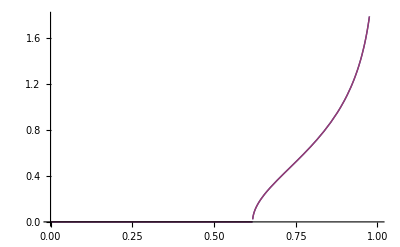

```mathematica
Plot[{Re[-((a-b r^2) √(a^2 p^2-r^2-2 a p^2 b r^2+p^2 b^2 r^4) ArcTan[(-a-b r^2)/(2 √(a b) √(a^2 p^2-r^2-2 a p^2 b r^2+b^2 p^2 r^4))])/(2 √(a b) √(r^2 (a-b r^2)^2-p^2 (a-b r^2)^4))],Re[(ArcTanh[(a+b r^2)/(2 √(a b) √(-a^2 p^2+r^2+2 a p^2 b r^2-b^2 p^2 r^4))])/(2 √(a b))]},{r,0,Sqrt[a/b]}]
```

```mathematica
((a-b r^2) √(p^2 a^2-r^2-2 p^2 a b r^2+p^2 b^2 r^4) ArcTan[(a+b r^2)/(2 √(a b) √(p^2 a^2-r^2-2 p^2 a b r^2+p^2 b^2 r^4))])/(2 √(a b) √(r^2 (a-b r^2)^2-p^2(a-b r^2)^4))
```

```mathematica
FullSimplify[(a^2 p^2-r^2-2 a p^2 b r^2+p^2 b^2 r^4)/(r^2 -p^2 (a-b r^2)^2)]
```

-1

```mathematica
Solve[s+c==-( I ArcTan[(-a-b r^2)/(2 √(a b) √(a^2 p^2-r^2-2 a p^2 b r^2+b^2 p^2 r^4))])/(2 √(a b)),r]
```

{{r→-√((a b)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 a b Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(4 a^2 b^2 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 √(-a^2 b^2 (1+4 a b p^2) Tanh[(2 (a b c+a b s))/(√(a b))]^2 (1-Tanh[(2 (a b c+a b s))/(√(a b))]^2)))/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2))},{r→√((a b)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 a b Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(4 a^2 b^2 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 √(-a^2 b^2 (1+4 a b p^2) Tanh[(2 (a b c+a b s))/(√(a b))]^2 (1-Tanh[(2 (a b c+a b s))/(√(a b))]^2)))/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2))},{r→-√((a b)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 a b Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(4 a^2 b^2 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(-a^2 b^2 (1+4 a b p^2) Tanh[(2 (a b c+a b s))/(√(a b))]^2 (1-Tanh[(2 (a b c+a b s))/(√(a b))]^2)))/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2))},{r→√((a b)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 a b Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(4 a^2 b^2 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(-a^2 b^2 (1+4 a b p^2) Tanh[(2 (a b c+a b s))/(√(a b))]^2 (1-Tanh[(2 (a b c+a b s))/(√(a b))]^2)))/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2))}}

```mathematica
v[r_]:=a-b r^2
```

```mathematica
r[s_]:=√((a b)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(2 a b Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)-(4 a^2 b^2 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(-a^2 b^2 (1+4 a b p^2) Tanh[(2 (a b c+a b s))/(√(a b))]^2 (1-Tanh[(2 (a b c+a b s))/(√(a b))]^2)))/(-b^2-4 a b^3 p^2 Tanh[(2 (a b c+a b s))/(√(a b))]^2))
```

```mathematica
FullSimplify[(p v[r[s]]^2)/r[s]^2]
```

-(8 a b p)/(1-4 a b p^2+(1+4 a b p^2) Cosh[4 √(a b) (c+s)])

```mathematica
Integrate[-(8 a b p)/(1-4 a b p^2+(1+4 a b p^2) Cosh[4 √(a b) (c+s)]),s]
```

-(√a √b ArcTan[2 √a √b p Tanh[2 √(a b) (c+s)]])/(√(a b))

```mathematica
θ[s_]:=ArcTan[2 √a √b p Tanh[2 √(a b) (c+s)]]+θ0
```

```mathematica
a=1;
b=1;
p=-10;
θ0=1;
c=0;
Manipulate[ParametricPlot[{Im[r[s]]Cos[θ[s]],Im[r[s]]Sin[θ[s]]},{s,x-.1,x+.1},PlotRange->{{-1,1},{-1,1}}],{x,-.2,.2}]
```

```mathematica
s=10
N[Im[r[s]]]
```

10

0.

```mathematica
Solve[s+c==(  ArcTan[(-a-b r^2)/(2 √(a b) p√(r^2-(a-b r^2)^2))])/(2 √(a b)),r]
```

{{r→-√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)-(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))},{r→√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)-(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))},{r→-√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))},{r→√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))}}

```mathematica
a=1
b=1
s=0.8
c=0
```

1

1

```mathematica
0.1
```

0.1

```mathematica
N[√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))]
```

1.61765

```mathematica
r[s_]:=√(-(a b)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 a b p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(4 a^2 b^2 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)+(2 √(a^2 b^2 (1+4 a b) p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2 (-1+p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2)))/(b^2+4 a b^3 p^2 Tan[(2 (a b c+a b s))/(√(a b))]^2))
v[r_]:=a-b r^2
```

```mathematica
FullSimplify[(p^2 v[r[s]]^2)/r[s]^2]
```

p^2 (1+(-1-4 a b)/(1+4 a b p^2 Tan[2 √(a b) (c+s)]^2))

```mathematica
Integrate[p^2 (1+(-1-4 a b)/(1+4 a b p^2 Tan[2 √(a b) (c+s)]^2)),s]
```

```mathematica
θ[s_]:=1/(√(a b) (-1+4 a b p^2))p^2 (2 a b (1+p^2) ArcTan[Tan[2 √(a b) (c+s)]]-√a √b (1+4 a b) p ArcTan[2 √a √b p Tan[2 √(a b) (c+s)]])
```

```mathematica
a=1;
b=1;
p=-10;
θ0=1;
c=0;
Manipulate[ParametricPlot[{r[s]Cos[θ[s]],r[s]Sin[θ[s]]},{s,x-.1,x+.1},PlotRange->{{-1,1},{-1,1}}],{x,-.2,.1}]
```

```mathematica
Solve[0==a^2 p^2-r^2-2 a p^2 b r^2+b^2 p^2 r^4,r]
```

{{r→(-1-√(1+4 a b p^2))/(2 b p)},{r→(1-√(1+4 a b p^2))/(2 b p)},{r→(-1+√(1+4 a b p^2))/(2 b p)},{r→(1+√(1+4 a b p^2))/(2 b p)}}

```mathematica
FullSimplify[((1+√(1+4 a b p^2))/(2 b p))^2-(p^2 a)/(1+p^2 b)]
```

a/(b+b^2 p^2)+(1+√(1+4 a b p^2))/(2 b^2 p^2)